# Proyecto

José Alfredo de León

## Definiciones

```mathematica
indices[L_]:=Flatten[Table[{i,j},{i,1,L-1},{j,i+1,L}],1]
```

```mathematica
Ν[L_]:=(L(L-1))/2
```

```mathematica
Ν[#]&/@Range[5]
```

{0,1,3,6,10}

```mathematica
SparseArray[indices[3]+1->{1,1,1},{3,3}]//MatrixForm
```

(0 | 1 | 1
0 | 0 | 1
0 | 0 | 0)

```mathematica
SparseArray[indices[4]+1->{1,1,1,1,1,1},{4,4}]//MatrixForm
```

(0 | 1 | 1 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

```mathematica
indices[5]
```

{{0,1},{0,2},{0,3},{0,4},{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

## Método Monte Carlo para modelo Sherrington-Kirkpatrick

Definimos una rutina para calcular la energía del sistema

```mathematica
SKEnergy[Jjk_,red_]:=Module[{L,SjSk},
L=Length[red];SjSk=Times@@red[[#]]&/@indices[L];
1/(L √L)Jjk.SjSk]
```

Creamos la red:

```mathematica
L=1000
red=RandomChoice[{-1,1},L];
ArrayPlot[{(red+1)/2}]
```

1000

-Graphics-

```mathematica
(*Generar los parámetros de interacción con números Gaussianos con desviación cero y varianza uno*)
Jjk=RandomVariate[NormalDistribution[0,1],{Ν[L]}];

(*Calcular la energía inicial de la configuración*)
E0=SKEnergy[Jjk,red];

(*Arreglo para guardar las energías*)
Energies={};

(*Elegir aleatoriamente un sitio inicial para voltear el espín*)
s=IntegerPart[1+RandomReal[]L];
red[[s]]=-red[[s]];

Do[
(*Print["Iteración "<>ToString[i]];
Print["Energía inicial: "<>ToString[E0]];
Print["Sitio a modificar: "<>ToString[s]];
RED=red;*)

(*Calcular la energía de la nueva configuración*)
Ef=SKEnergy[Jjk,red];EF=Ef;
(*Print["Energía final: "<>ToString[Ef]];
Print[Ef<E0];*)

(*Si la energía disminuye (Ef<E0), entonces la red se queda con el cambio. De lo contrario, el cambio se queda con probabilidad p=Exp[-(Ef-E0)]*)
If[Ef<E0,E0=Ef,If[RandomReal[]<0,E0=Ef,red[[s]]==-red[[s]]]];

(*Guardar la energía de la iteración*)
AppendTo[Energies,Ef];

(*Elegir movernos aleatoriamente el espín a la derecha o la izquierda para voltear*)
(*step=(-1)^RandomInteger[];
Which[s+step!=L && s+step!=0,s=s+step,s+step>L,s=0,s+step<0,s=L];
red[[s]]=-red[[s]];*)

(*s=IntegerPart[1+RandomReal[]L];
red[[s]]=-red[[s]];*)

s=IntegerPart[RandomVariate[NormalDistribution[s,2]]];
If[s>L,s=s-L,If[s<0,s=L+s]];
red[[s]]=-red[[s]];

(*
Print["¿Bajó la energía? "<>ToString[E0<EF]];
Print["¿Se modificó la red? "<>ToString[RED!=red]];
Print[];*)
,{i,1000}]
```

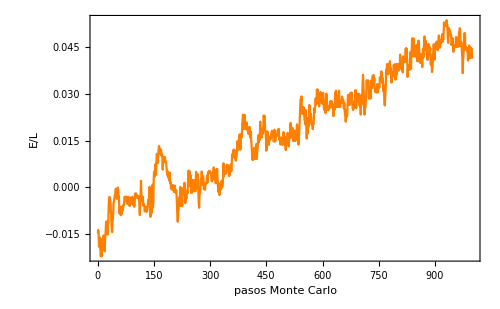

```mathematica
fig=ListPlot[Energies,Joined->True,PlotRange->All,PlotStyle->Orange,Frame->True,LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"pasos Monte Carlo","E/L"},ImageSize->500]
```

```mathematica
Export["/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/figs_avance/intento_014.pdf",fig]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/figs_avance/intento_014.pdf

```mathematica
Table[RandomReal[]<0,10]
```

{False,False,False,False,False,False,False,False,False,False}